#### Gr. 1

Zad. 1

-48 x-12 x^2+8 x^3+3 x^4

-48-24 x+24 x^2+12 x^3

{{x→-2},{x→-√2},{x→√2}}

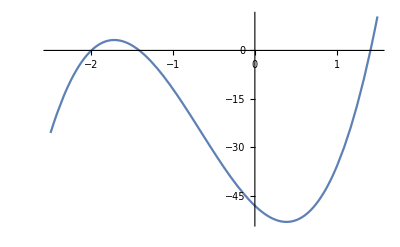

```mathematica
(x+2)(x^2-2)//Expand;
Integrate[%,x]12//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-2.5,1.5}]
```

Zad. 2

```mathematica
Integrate[3/x^2+2/Sqrt[x],x]
Integrate[Sin[x]^5 Cos[x],x]
Integrate[x Cos[10 x],x]
```

-3/x+4 √x

Sin[x]^6/6

1/100 Cos[10 x]+1/10 x Sin[10 x]

Zad. 3

```mathematica
2/(x-1)+3/(x+2)//Together;
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(1+5 x)/(-2+x+x^2)

2 Log[1-x]+3 Log[2+x]

#### Gr. 1I

Zad. 1

72 x-18 x^2-8 x^3+3 x^4

72-36 x-24 x^2+12 x^3

{{x→2},{x→-√3},{x→√3}}

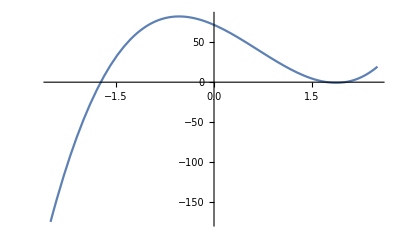

```mathematica
(x-2)(x^2-3)//Expand;
Integrate[%,x]12//Expand
D[%,x]
Solve[%==0,x]
Plot[%%,{x,-2.5,2.5}]
```

Zad. 2

```mathematica
Integrate[3Cos[x]-3/x^4,x]
Integrate[1/(ArcSin[x]Sqrt[1-x^2]),x]
Integrate[x^7 Log[x],x]
```

1/x^3+3 Sin[x]

Log[ArcSin[x]]

-x^8/64+1/8 x^8 Log[x]

Zad. 3

```mathematica
2/(x+2)+3/(x+2)^2//Together;
Numerator[%]/Expand[Denominator[%]]
Integrate[%,x]
```

(7+2 x)/(4+4 x+x^2)

-3/(2+x)+2 Log[2+x]